```mathematica
Clear[r1,r2]
```

```mathematica
(* given bubbles of radii r1 and r2, the have stable equilibrium if
they are seperated either by L > (r1+r2) or by L = √(r1^2-r1 r2+r2^2)
defining weird power function: d_b(p) = 1/r_b dist(p,center of b)^2 - r_b, and define the bubble by p st d_b(p) < 0. When two bubbles are correct distance apart, this gives the correct bubble wall *)
```

```mathematica
Solve[ x^2/r- r== (l-x)^2/r -r,x]
```

{{x→l/2}}

```mathematica
x1[r1_,r2_,l_] = (-l/r2-(√(l^2-r1^2+2 r1 r2-r2^2))/(√r1 √r2))/(1/r1-1/r2);
x2[r1_,r2_,l_]=(-l/r2+(√(l^2-r1^2+2 r1 r2-r2^2))/(√r1 √r2))/(1/r1-1/r2);
```

```mathematica
FullSimplify[x2[r1,r2,l]]
```

(l r1-√r1 √r2 √((l+r1-r2) (l-r1+r2)))/(r1-r2)

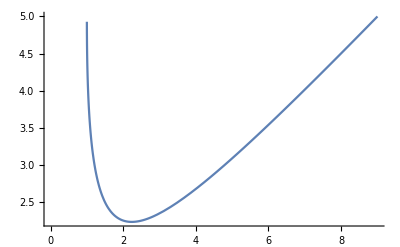

```mathematica
Plot[x2[5,4,l],{l,0,9}]
```

```mathematica
FullSimplify[{{x->},{x->(-l/r2+(√(l^2-r1^2+2 r1 r2-r2^2))/(√r1 √r2))/(1/r1-1/r2)}}]
```

{{x→(l r1+√r1 √r2 √((l+r1-r2) (l-r1+r2)))/(r1-r2)},{x→(l r1-√r1 √r2 √((l+r1-r2) (l-r1+r2)))/(r1-r2)}}

```mathematica
CForm[(l r1+√r1 √r2 √((l+r1-r2) (l-r1+r2)))/(r1-r2)]
```

(l*r1 + Sqrt(r1)*Sqrt(r2)*Sqrt((l + r1 - r2)*(l - r1 + r2)))/(r1 - r2)

```mathematica
(* now area *)
```

```mathematica
(* bubble r1 and bubble r2, seperated L *)
```

```mathematica
(* define r10 and r20 *)
```

```mathematica
Solve[{Sin[t1] r1 == Sin[t2]r2, Cos[t1]r1 +Cos[t2]r2 == L},{t1,t2}]
```

```mathematica
Clear[t1]
```

```mathematica
t1[r1_,r2_,L_]=ArcTan[L^2+r1^2-r2^2,√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2))];
```

```mathematica
FullSimplify[D[t1[r1,r2,L],L]]
```

-(L^2-r1^2+r2^2)/(L √((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2)))

```mathematica
Clear[t1]
```

```mathematica
A1[r1_,r2_,L_] = FullSimplify[Pi r1^2 - ( t1[r1,r2,L]/(2 Pi)Pi r1^2 - Sin[t1[r1,r2,L]]Cos[t1[r1,r2,L]] r1^2/2)*2];
```

```mathematica
Solve[{D[A1[r1,r2,L],L]dl -  D[A1[r1,r2,L],r1]dr1 - D[A1[r1,r2,L],r2]dr2 == 0,D[A1[r2,r1,L],L]dl -  D[A1[r2,r1,L],r1]dr1 - D[A1[r2,r1,L],r2]dr2 == 0},{dr1,dr2}]
```

```mathematica
dadl[r1_,r2_,L_] = D[A1[r2,r1,L],L];
dadr1[r1_,r2_,L_] = D[A1[r2,r1,L],r1];
dadr2[r1_,r2_,L_] = D[A1[r2,r1,L],r2];
```

```mathematica
r1 = 1.8; r2 = 2; L = 3.5;
```

```mathematica
Clear[Q,t1,t2]
```

```mathematica
Q=√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2))
t1=ArcTan[L^2+r1^2-r2^2,Q]
t2 = ArcTan[L^2-r1^2+r2^2,Q]
```

5.17106

0.422895

0.378322

```mathematica
Clear[t1,t2,Q]
```

```mathematica
dr1p  = (((L^4+(r1-r2) (r1+r2) (r1^2-r2^2+π Q)-L^2 (2 r1^2+2 r2^2+π Q)+Q (L^2-r1^2+r2^2) t2))/(2 L r1 (2 π (L^2 π+Q)-t1 (Q+2 L^2 (π-t2))-(2 L^2 π+Q) t2)));
dr2p  = (((L^4+(r1-r2) (r1+r2) (r1^2-r2^2-π Q)-L^2 (2 r1^2+2 r2^2+π Q)+Q (L^2+r1^2-r2^2)t1))/(2 L r2 (2 π (L^2 π+Q)-t1 (Q+2 L^2 (π-t2))-(2 L^2 π+Q) t2)));
```

```mathematica
dr1p
```

-0.0794535

```mathematica
dr2p
```

-0.0633136

```mathematica
.262-.317
```

```mathematica
-0.05499999999999999/dt
```

-0.055/dt

```mathematica
CForm[FullSimplify[dr2p]]
```

(Power(L,4) - Power(L,2)*(Pi*Q + 2*(Power(r1,2) + Power(r2,2)) - Q*t1) + (r1 - r2)*(r1 + r2)*(-(Pi*Q) + Power(r1,2) - Power(r2,2) + Q*t1))/
   (2.*L*r2*(2*Power(L,2)*(Pi - t1)*(Pi - t2) + Q*(2*Pi - t1 - t2)))

```mathematica
dr2p
```

-0.0633136

```mathematica
dr1p
```

-0.0794535

```mathematica
dr2[r1,r2,L]
```

-0.0794535

```mathematica
dr1[r1,r2,L]
```

-0.0633136

```mathematica
dr1[r1_,r2_,L_] = (( (L^4+(r1-r2) (r1+r2) (r1^2-r2^2+π √(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)))-L^2 (2 r1^2+2 r2^2+π √(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)))+√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)) (L^2-r1^2+r2^2) ArcTan[L^2-r1^2+r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))]))/(2 L r1 (2 π (L^2 π+√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)))-ArcTan[L^2+r1^2-r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))] (√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2))+2 L^2 (π-ArcTan[L^2-r1^2+r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))]))-(2 L^2 π+√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2))) ArcTan[L^2-r1^2+r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))])));
```

```mathematica
dr2[r1_,r2_,L_]= (( (L^4+(r1-r2) (r1+r2) (r1^2-r2^2-π √(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)))-L^2 (2 r1^2+2 r2^2+π √(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)))+√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)) (L^2+r1^2-r2^2) ArcTan[L^2+r1^2-r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))]))/(2 L r2 (2 π (L^2 π+√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2)))-ArcTan[L^2+r1^2-r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))] (√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2))+2 L^2 (π-ArcTan[L^2-r1^2+r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))]))-(2 L^2 π+√(-(L-r1-r2) (L+r1-r2) (L-r1+r2) (L+r1+r2))) ArcTan[L^2-r1^2+r2^2,√((L+r1-r2) (L-r1+r2) (-L+r1+r2) (L+r1+r2))])));
```

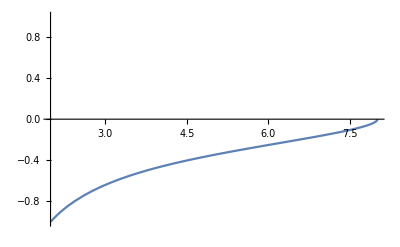

```mathematica
Plot[dr1[3,5,x],{x,0,8},PlotRange->{-1,1}]
```

```mathematica
testf[x1_,x2_,x_] = FullSimplify[-(√2 √x x2 √(x1 x2 (x1+x2)))/(x1 (x1+x2)^2 (π+ⅈ Log[(x1^2+x1 x2)/(√(x1^2 (x1+x2)^2))]))];
```

```mathematica
testdr1[x1_,x2_,x_] = -(√2 √x x1 x2^3)/((x1 x2 (x1+x2))^(3/2) π);
testdr2[x1_,x2_,x_] = -(√2 √x x1^3 x2)/((x1 x2 (x1+x2))^(3/2) π);
```

```mathematica
CForm[-(√2 √x x1 x2^3)/((x1 x2 (x1+x2))^(3/2) π)]
```

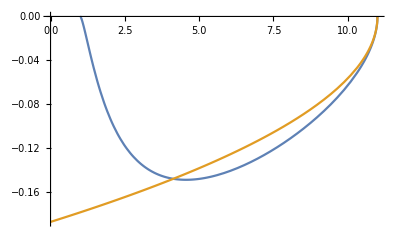

```mathematica
Plot[{dr1[6,5,x],testdr1[6,5,11-x]},{x,0,11}]
```

```mathematica
Q(u/(1+u),1-u/(1+u))-(u/(1+u))x-(1-u/(1+u))y
```

```mathematica
Sum[(-1)^n/( 2n + 3),{n,0,Infinity}]
```

1-π/4

```mathematica
q[u_] = 1+a u;
```

```mathematica
Solve[q[u]-(u/(1+u))x-(1-u/(1+u))y == 0,u]
```

{{u→(-1-a+x-√((1+a-x)^2-4 a (1-y)))/(2 a)},{u→(-1-a+x+√((1+a-x)^2-4 a (1-y)))/(2 a)}}

```mathematica
Clear[d,f]
```

```mathematica
test[x_,y_]=(c+a x+b y-√(e+x^2 + y^2))/(d x + f y + g);
```

```mathematica
Expand[FullSimplify[D[test[x,y],x]- test[x,y]D[test[x,y],y]]]
```

(c^2 f)/(g+d x+f y)^3+(e f)/(g+d x+f y)^3-(b c g)/(g+d x+f y)^3-(b c d x)/(g+d x+f y)^3+(2 a c f x)/(g+d x+f y)^3-(a b g x)/(g+d x+f y)^3-(a b d x^2)/(g+d x+f y)^3+(f x^2)/(g+d x+f y)^3+(a^2 f x^2)/(g+d x+f y)^3+(b c f y)/(g+d x+f y)^3-(g y)/(g+d x+f y)^3-(b^2 g y)/(g+d x+f y)^3-(d x y)/(g+d x+f y)^3-(b^2 d x y)/(g+d x+f y)^3+(a b f x y)/(g+d x+f y)^3-(c d)/(g+d x+f y)^2+(a g)/(g+d x+f y)^2-(b d y)/(g+d x+f y)^2+(a f y)/(g+d x+f y)^2+(c g y)/((g+d x+f y)^3 √(e+x^2+y^2))+(c d x y)/((g+d x+f y)^3 √(e+x^2+y^2))+(a g x y)/((g+d x+f y)^3 √(e+x^2+y^2))+(a d x^2 y)/((g+d x+f y)^3 √(e+x^2+y^2))+(c f y^2)/((g+d x+f y)^3 √(e+x^2+y^2))+(b g y^2)/((g+d x+f y)^3 √(e+x^2+y^2))+(b d x y^2)/((g+d x+f y)^3 √(e+x^2+y^2))+(a f x y^2)/((g+d x+f y)^3 √(e+x^2+y^2))+(b f y^3)/((g+d x+f y)^3 √(e+x^2+y^2))-(g x)/((g+d x+f y)^2 √(e+x^2+y^2))-(d x^2)/((g+d x+f y)^2 √(e+x^2+y^2))-(f x y)/((g+d x+f y)^2 √(e+x^2+y^2))-(2 c f √(e+x^2+y^2))/(g+d x+f y)^3+(b g √(e+x^2+y^2))/(g+d x+f y)^3+(b d x √(e+x^2+y^2))/(g+d x+f y)^3-(2 a f x √(e+x^2+y^2))/(g+d x+f y)^3-(b f y √(e+x^2+y^2))/(g+d x+f y)^3+(d √(e+x^2+y^2))/(g+d x+f y)^2